```mathematica
(*Functions*)
AngleWrap[θrad_?NumericQ]:=Module[{θ},θ=Mod[θrad+π,2 π];
If[θ<0,θ=θ+2 π;];
θ=θ-π];
Saturation[variable_, limit_]:=Return[Which[variable>limit,limit, variable<-limit, -limit,-limit≤ variable≤ limit, variable]];
xtraj[InitCond_, to_,tf_,u_]:=Module[{eq1,sol},
eq1=Join[ Thread[Flatten[dX]== Flatten[f[X,u]]],InitCon];
sol=X/.First@NDSolve[{eq1[[2]],eq1[[4;;]]},Flatten[X], {t,to,tf},Method-> "DiscontinuityProcessing"-> False];
(*sol[[1,1]]=AngleWrap[sol[[1,1]]];*)
Return[sol];
]
ρsolve[xsol_,to_,tf_]:=Module[{ρ1,ρ2,ρ3,ρ4,ρ,dρ,eq2,InitCon2,ρsol,xwrap=xsol},
xwrap[[1,1]]=AngleWrap[xsol[[1,1]]];
ρ={{ρ1[t],ρ2[t],ρ3[t],ρ4[t]}}ᵀ;
dρ=D[ρ,t];
eq2 = Thread[Flatten[dρ]==Flatten[(-asym-Asymᵀ.ρ/.alat[t]-> 0)/.Thread[Flatten[X]-> Flatten[xwrap]]]];
InitCon2 = Thread[Flatten[ρ/.t-> tf]==0];
ρsol=ρ/.First@NDSolve[Join[eq2,InitCon2],Flatten[ρ],{t,to,tf},Method-> "DiscontinuityProcessing"-> False](*3b*);
Return[ρsol];
]
uInterval[ControlInterval_, SimulationInterval_]:=Module[{A=ControlInterval,  B=SimulationInterval, tauo, tauf},
tauf= Max[B];
tauo = Min[B];
(* Bound control within (to, to+ts) range: (Min[A], Max[A]) *)
If[Min[A]≥Min[B], tauo= Min[A]];
If[Max[A]≤Max[B], tauf = Max[A]];
Return[List[tauo, tauf]];
];
MinDisc[f_,t0_,tf_]:=Module[{list,index,min},
list=Table[Flatten[{t,f}],{t,t0,tf,0.01}](*7c*);
index = Position[list[[1;;,2]],Min[list[[1;;,2]]]][[1,1]];
min=list [[index,1]];
Return[min]];
Cost[Xsol_,U_,to_,tf_]:=Module[{c,X2=Xsol},X2[[1,1]]=AngleWrap[X2[[1,1]]];
c=NIntegrate[L[X2,U]/.Thread[Flatten[X]-> Flatten[X2]],{t,to,tf}](*+1/2*(X/.xsol/.t-> tf - Xd[tf])ᵀ.P1.(X/.xsol/.t-> tf - Xd[tf])*)[[1,1]];
Return[c];
];
SACcalc[to_,tf_,InitCon_,U1_]:=Module[{γ,Δtinit,β,tcalc,kmax,xsol,ρsol,J1init,ΔJmin,αd,Λ,u2,dJdλ,Jτm,τm,u2τ,k,ω,J1new,λ,τo,τf,u1temp,xsol2,U1new,xcurr},
(*SAC initialization and local parameters*)
γ = -5(*-5,-10,-15,-20*);
ΔJmin = -200;
Δtinit = 0.2;
β=0.55(*0.7*);
tcalc=0;
kmax = 6;

xsol =xtraj[InitCon,to,tf,U1](*3a*);
ρsol=ρsolve[xsol,to,tf](*3b*);
J1init =Cost[xsol,U1,to,tf](*4*);
ΔJmin = 0(*-0.05*J1init*);
αd=γ*J1init(*5*);
Λ=hxᵀ.ρsol.ρsolᵀ.hx/.Thread[Flatten[X]-> Flatten[xsol]](*6a*);
u2=Inverse[Λ+Rᵀ].(Λ.U1+hxᵀ.ρsol*αd)/.Thread[Flatten[X]-> Flatten[xsol]](*6b*);
dJdλ = ρsolᵀ.(f[xsol,u2]-f[xsol,U1])(*7a*);
Jτm= Norm[u2]+dJdλ+(t-to)^β(*7b*);
τm=MinDisc[Jτm,to,tf];
u2τ={{Saturation[(u2/.t-> τm)[[1,1]],umax]}}(*8*);

k=0; ω=0.55;J1new = Infinity (*9*);

While[J1new-J1init>ΔJmin && k≤ kmax,
     λ=Δtinit*ω^k(*10a*);
     {τo,τf}=Chop[{τm-λ/2,τm+λ/2}](*10b*);
     {τo,τf}=uInterval[Interval[to,to+ts(*use T for iSAC*)],Interval[τo,τf]];
     u1temp = Piecewise[{{u2τ[[1,1]],τo≤ t≤ τf}},U1[[1,1]]];
      xsol2 = xtraj[InitCon,to,tf,{{u1temp}}](*10c*);
     J1new = Cost[xsol2,{{u1temp}},to,tf](*10d*);
     k++(*10e*);
](*end inner while*);


u1temp=PiecewiseExpand[u1temp];
U1new={{u1temp}}(*11*);
xcurr = Flatten[xtraj[InitCon,to,tf,{{u1temp}}]/.t-> (to+ts)](*10c*);
Return[{xcurr,U1new}];
];
```

```mathematica
Quit[]
```

```mathematica
(*initional condition offset*)
δ=0.001;
(*system parameters*)
m=0.1;
B=0.01;
g=9.81;
h =2.0;
Tf=15;
umax = 20;
X={{ϕ[t]},{ϕ'[t]},{x[t]},{x'[t]}};
dX = D[X,{t,1}];
U= {{alat[t]}};
f[x_,u_]:={{x[[2,1]]},{g/h*Sin[x[[1,1]]]-u[[1,1]]*Cos[x[[1,1]]]/h+B*x[[1,1]]/(m*h^2)},{x[[4,1]]},{u[[1,1]]}}(*hard-coded dynamics*);
hx={{0,-Cos[ϕ[t]]/h,0,1}}ᵀ(*Linear operator on the control input*);
InitCon = {ϕ[0]==Pi+δ,ϕ'[0]==0.,x[0]==0.0,x'[0]==0.0};
(*cost specifications*)
ϕd[t_]:=0//N
dϕd[t_]:=D[ϕd[t],t]//N
Xd[t_]:={{ϕd[t]},{dϕd[t]},{0},{0}};
Q=DiagonalMatrix[{200.,0.,20.,1.}];
Qn = Q;
Qr = Q;
R={{0.3}};
Rn = R;
Rr = R;
P1 = {{0,0},{0,0}};
P1n = P1;
P1r = P1;
L[X_,U_]:=Module[{X2=X,l},
l=1/2((X2-Xd[t])ᵀ.Q.(X2-Xd[t]))+1/2*Uᵀ.R.U;
Return[l];];

(*Setting up the linearization*)
Asym = D[f[X,U],Xᵀ];
Bsym = D[f[X,U],Uᵀ];
asym = D[L[X,U],{X,1}][[1,1]];
bsym = D[L[X,U],U][[1]];
Ta[R_]:=Table[R[[i,1]],{i,1,4}]
Asym =Ta[Asym];
Bsym =Ta[Bsym];

(*Sequential Action Control*)
 (*list for saving x*)
xlist ={{Pi+δ,0,0,0}};
(*SAC initialization and time parameters*)
tcurr=0;
U1 = 0*U(*nominal control*);
T=1.2;
ts =1/30;
i=0;
Print[Dynamic[i]];
Print["Current time ",Dynamic[Round[tcurr//N,0.01]]];
Print["θ= ",Dynamic[AngleWrap[xcurr[[1]]] ]];

While[tcurr<Tf ,
i++(*1*);
{to,tf}={tcurr,tcurr+T}(*2*)(*pass to function t0,tf,InitCon,U1*);
(*updates*)
{xcurr,U1}=SACcalc[to,tf,InitCon,U1];
tcurr=tcurr+ts;
InitCon=Thread[Flatten[X/.t-> tcurr]==xcurr];
AppendTo[xlist,xcurr];

](*end while*)
```

Current time

θ=

-Graphics-

$Aborted

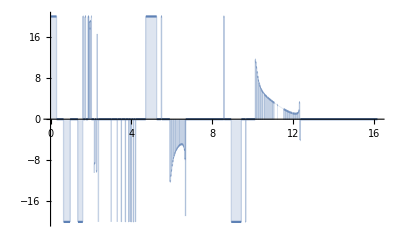

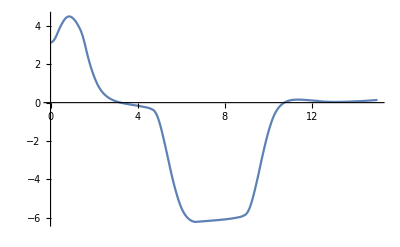

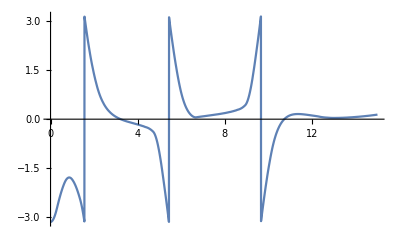

```mathematica
uplot[τ_]:=(U1/.t-> τ)[[1,1]];
Plot[uplot[t],{t,0,tf}, Filling->Axis,PlotRange-> Full]

xsol={{ListInterpolation[xlist[[;;,1]],{{0,Tf}}][t],ListInterpolation[xlist[[;;,2]],{{0,Tf}}][t],ListInterpolation[xlist[[;;,3]],{{0,Tf}}][t],ListInterpolation[xlist[[;;,4]],{{0,Tf}}][t]}}ᵀ;
Plot[Flatten[xsol][[1]],{t,0,Tf},PlotRange->Full]
Plot[AngleWrap[Flatten[xsol][[1]]],{t,0,Tf},PlotRange->Full]
```

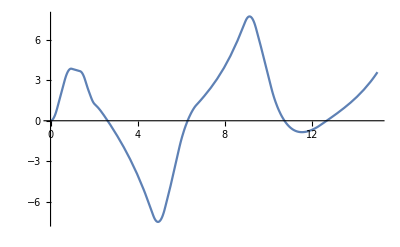

IntervalIntersection[Interval[{τo,τf}],Interval[{15,16.1667}]]

```mathematica
xc[τ_]:=(xsol[[3]]/.t-> τ)[[1]];

xp[τ_]:=(xsol[[3]]+h*Sin[xsol[[1]]]/.t-> τ)[[1]];
yp[τ_]:=(h*Cos[xsol[[1]]]/.t-> τ)[[1]];
Plot[xc[t],{t,0,Tf}]
Animate[Graphics[{{Green,Rectangle[{xc[t]-0.05,-0.05},{xc[t]+0.05,0.05}]},{Black,Line[{{xp[t],yp[t]},{xc[t],0}}]},{Black,Disk[{xp[t],yp[t]},0.05]}},PlotRange-> {{-10,10},{-1,1}},Axes->True,PlotLabel->"X-Z Plane"],{t,0,Tf},AnimationRate-> 1]
k=IntervalIntersection[Interval[{τo,τf}],Interval[{tcurr,tf}]]
```

```mathematica
NIntegrate[L[xsol,U1],{t,to,tf}]
Cost[xsol,U1,to,tf]
```

{{61.0312}}

56.0747

```mathematica
Jτmlist=Table[Flatten[{t,Jτm}],{t,to,tf,0.01}];
Dimensions[Jτmlist]
Jτmlist[[1;;,2]]
Position[Jτmlist[[1;;,2]],Min[Jτmlist[[1;;,2]]]][[1,1]]
Jτmlist [[48,1]]
Chop[NMinimize[{Jτm,to≤ t≤ tf},t][[2,1,2]]]
```

{121,2}

{-159.545,-145.962,-129.401,-108.821,-82.7974,-49.3639,-6.06245,48.9793,111.616,152.8,93.0268,85.6542,153.125,119.379,61.7962,9.76397,-31.7803,-64.1619,-89.5259,-109.665,-125.904,-139.193,-150.217,-159.472,-167.322,-174.041,-179.838,-184.872,-189.269,-193.127,-196.525,-199.528,-202.186,-204.542,-206.633,-208.485,-210.125,-211.572,-212.843,-213.953,-214.913,-215.734,-216.424,-216.989,-217.435,-217.765,-217.984,-218.093,-218.093,-217.983,-217.763,-217.431,-216.984,-216.417,-215.724,-214.9,-213.935,-212.819,-211.541,-210.085,-208.434,-206.62,-204.701,-202.668,-200.515,-198.233,-195.813,-193.244,-190.516,-187.616,-184.532,-181.25,-177.753,-174.024,-170.046,-165.796,-161.254,-156.395,-151.192,-145.616,-139.635,-133.217,-126.323,-118.916,-110.953,-102.39,-93.1841,-83.2883,-72.659,-61.2551,-49.0419,-35.9951,-22.1066,-7.39134,8.10374,24.2879,41.0149,58.069,75.1519,91.8741,107.753,122.221,134.655,144.42,150.936,153.75,152.614,147.534,138.796,126.941,112.705,96.9388,80.5194,64.2757,48.9366,35.104,23.2482,13.7178,6.75659,2.52296,1.10548}

48

0.47

0.474966